# Project

Facial images convey many important human characteristics, such as identity, gender, expression, age, and ethnicity. 
Representative examples including face recognition, facial expression recognition, age estimation, gender classification and ethnicity recognition.

Objective:
Identify the kinship using faces.

Dataset:

Labeled faces in the Wild

Import data

```mathematica
data=Import[""]
```

import the code

```mathematica
<<Project`
```

```mathematica
?Classify
```

Classify[{example_1→class_1,example_2→class_2,…}] generates a ClassifierFunction[…] based on the examples and classes given.
Classify[{example_1,example_2,…}→{class_1,class_2,…}] also generates a ClassifierFunction[…] based on the examples and classes given.
Classify[<|class_1→{example_11,example_12,…},class_2→{example_21,…},…|>] generates a ClassifierFunction[…] based on an association of classes with their examples.
Classify[training,data] attempts to classify data using a classifier function deduced from the training set given.
Classify[name,data] attempts to classify data using the built-in classifier function represented by "name".
Classify[…,data,prop] gives the specified property of the classification associated with data.
Classify[classifier,opts] takes an existing classifier function and modifies it with the new options given.

```mathematica
ImageSize
```

```mathematica
MorphologicalComponents
```

```mathematica
ImageResize
```

```mathematica
ImageDimensions[-Graphics-]
```

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
ImageDimensions[-Graphics-]
```

{64,64}

```mathematica
FindFaces
```

```mathematica
FeatureExtraction
```

```mathematica
MorphologicalPerimeter
```

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son"]
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son

```mathematica
ClearAll[dataFatherSon];
```

```mathematica
fatherSon=Import["fs*"];
```

```mathematica
createCouples[ imgs_List ] := Partition[ imgs , 2 ] ;

fakeCouples[ imgs_List ] := createCouples[
                                          RotateLeft[ imgs , 1 ]
                                         ];
                                                       
createClasses[ imgs_List, { n_Integer, m_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> "couples" ,
                                     #2 -> "fake couples"
                                    } & ,
                                    
                                   { Take[
                                          createCouples[ imgs ],
                                          {n, m}
                                          ],
                                     Take[
                                          fakeCouples[ imgs ],
                                          {n, m}
                                          ]
                                   }
                                 ]
                               ];
```

```mathematica
trainingSet = createClasses[fatherSon,{11,110}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
validationSet = createClasses[fatherSon,{1,10}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
testSet = createClasses[fatherSon,{111,174}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
cl=Classify[
trainingSet, 
ValidationSet-> validationSet
 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,testSet]
```

ClassifierMeasurementsObject[…]

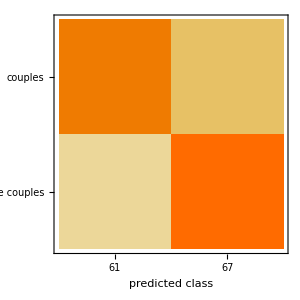

```mathematica
%["ConfusionMatrixPlot"]
```

```mathematica
cl
```

```mathematica
convP = Take[NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"], {1, "4b22"}];
```

```mathematica
fmodel2 = NetGraph[{convP, convP, CatenateLayer[], FlattenLayer[], LinearLayer[128], Ramp, LinearLayer[], SoftmaxLayer[]}, {1->3, 2->3, 3->4, 4->5, 5->6, 6->7->8}, "Output"->5];
```

```mathematica
net = NetInitialize[fmodel2]
```

NetGraph[<>]

```mathematica
net
```

NetGraph[<>]

```mathematica
model = NetTrain[net,data , LearningRateMultipliers->{"1"->None, "2"-> None, _->1}]
```

NetTrain::invencin: Invalid input, input is neither a 2D image or a File.

$Failed

```mathematica
NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"]
```

NetChain[<>]

Proposal 1
Binary classification

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son

{{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon}